```mathematica
Factor[-54 a+10 a b+8 a c-a (-b+b c)+22 a d-b (-a+a d)-c (-a+a d)-4 a (-b+b d)-2 a (-c+c d)+c (2 a-a b-a d+a (-b+b d))+2 a e-(-a+a b) e-(-a+a c) e-4 (-a+a d) e+c (2 a-2 a d+(-a+a d) e)+a (2 b-2 b d+(-b+b d) e)+12 a f-b (-a+a f)-2 e (-a+a f)-a (-b+b f)-2 a (-c+c f)-6 a (-d+d f)+b (2 a-a d-a f+a (-d+d f))+2 c (2 a-a d-a f+a (-d+d f))+a (2 b-b d-b f+b (-d+d f))+2 a (2 d-d e-d f+e (-d+d f))-b (-6 a+2 a c+2 a d-a (-c+c d)+2 a f-a (-c+c f)-a (-d+d f)+c (2 a-a d-a f+a (-d+d f)))-b (-6 a+3 a d+a e-(-a+a d) e+2 a f-e (-a+a f)-a (-d+d f)+a (2 d-d e-d f+e (-d+d f)))-a (-6 c+3 c d+c e-(-c+c d) e+2 c f-e (-c+c f)-c (-d+d f)+c (2 d-d e-d f+e (-d+d f)))+a (18 b-5 b c-8 b d+c (-b+b d)+b (-c+c d)-b e+(-b+b c) e+2 (-b+b d) e-c (2 b-2 b d+(-b+b d) e)-4 b f+e (-b+b f)+b (-c+c f)+2 b (-d+d f)-c (2 b-b d-b f+b (-d+d f))-b (2 d-d e-d f+e (-d+d f))+b (-6 c+3 c d+c e-(-c+c d) e+2 c f-e (-c+c f)-c (-d+d f)+c (2 d-d e-d f+e (-d+d f))))]
```

a (-1+b) (-2+c) (-27+16 d+5 e-4 d e+6 f-4 d f-e f+d e f)

```mathematica
CoefficientList[-27+5 e+6 f-e f+d (16-4 e-4 f+e f),d]
```

{-27+5 e+6 f-e f,16-4 e-4 f+e f}

```mathematica
BreakUp[exp_,syms_]:=Block[{reorder, coeff, s},
If[syms=={}||Length[syms]==1, Return [exp]];
s=syms[[1]];
reorder = Collect[exp,s];
coeff=CoefficientList[reorder,s];
coeff=Map[BreakUp[#,Rest[syms]]&, coeff];
Fold [Plus,Table[Framed[coeff[[k]]]*s^(k-1),{k,Length[coeff]}]]
]
```

```mathematica
BreakUp[(-27+16 d+5 e-4 d e+6 f-4 d f-e f+d e f),{d,e,f}]
```

e f -1+5+-27+f 6+d e -4+f 1+f -4+16

```mathematica
Table[Symbol[MyLetter[k]],{k,6}]
```

{a,b,c,d,e,f}

```mathematica
Expand[a (-1+b) (-2+c) (-27+16 d+5 e-4 d e+6 f-4 d f-e f+d e f)]
```

-54 a+54 a b+27 a c-27 a b c+32 a d-32 a b d-16 a c d+16 a b c d+10 a e-10 a b e-5 a c e+5 a b c e-8 a d e+8 a b d e+4 a c d e-4 a b c d e+12 a f-12 a b f-6 a c f+6 a b c f-8 a d f+8 a b d f+4 a c d f-4 a b c d f-2 a e f+2 a b e f+a c e f-a b c e f+2 a d e f-2 a b d e f-a c d e f+a b c d e f

```mathematica
BreakUp[-54 a+54 a b+27 a c-27 a b c+32 a d-32 a b d-16 a c d+16 a b c d+10 a e-10 a b e-5 a c e+5 a b c e-8 a d e+8 a b d e+4 a c d e-4 a b c d e+12 a f-12 a b f-6 a c f+6 a b c f-8 a d f+8 a b d f+4 a c d f-4 a b c d f-2 a e f+2 a b e f+a c e f-a b c e f+2 a d e f-2 a b d e f-a c d e f+a b c d e f,Table[Symbol[MyLetter[k]],{k,6}]]
```

Fold[Plus,{}]+a b c d 16-4 f+e -4+f+e 5-f+-27+6 f+54-12 f+e -10+2 f+d e 8-2 f+-32+8 f+c 27-6 f+e -5+f+d e 4-f+-16+4 f+d 32-8 f+e -8+2 f+e 10-2 f+-54+12 f

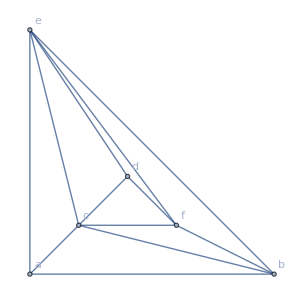
a (-1+b) (-2+c) (-27+16 d+5 e-4 d e+6 f-4 d f-e f+d e f)1
(-3+x)^3 (-2+x) (-1+x) x0
-Graphics-

```mathematica
With[{g=ReadGrof[3]},Framed[Column[{Pane[Labeled[Style[Factor[CalculateInOutFormulaAll[g]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,4]/24,Red,Bold]],500],
Pane[Labeled[Style[Factor[ChromaticPolynomial[g,x]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,3],Red,Bold]],500],Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->VertexNames[VertexCount[g]]]}]]]
```

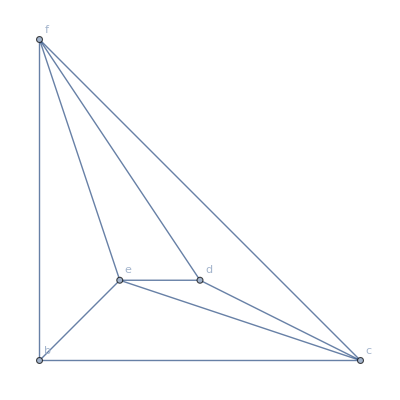
b (-1+c) (-18+12 d+5 e-4 d e+4 f-3 d f-e f+d e f)1
(-3+x)^2 (-2+x) (-1+x) x0
-Graphics-

```mathematica
With[{g=VertexDelete[ReadGrof[3],1]},Framed[Column[{Pane[Labeled[Style[Factor[CalculateInOutFormulaAll[g]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,4]/24,Red,Bold]],500],
Pane[Labeled[Style[Factor[ChromaticPolynomial[g,x]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,3],Red,Bold]],500],Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->VertexNames[VertexCount[g]+1]]}]]]
```

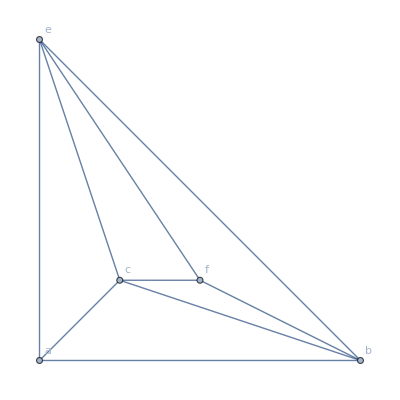
a (-1+b) (-2+c) (-3+e) (-3+f)1
(-3+x)^2 (-2+x) (-1+x) x0
-Graphics-

```mathematica
With[{g=VertexDelete[ReadGrof[3],4]},Framed[Column[{Pane[Labeled[Style[Factor[CalculateInOutFormulaAll[g]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,4]/24,Red,Bold]],500],
Pane[Labeled[Style[Factor[ChromaticPolynomial[g,x]],LineIndent->0,TextAlignment->Left],Style[ChromaticPolynomial[g,3],Red,Bold]],500],Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->VertexNames[VertexCount[g]+1]]}]]]
```

```mathematica
((-27+16 d+5 e-4 d e+6 f-4 d f-e f+d e f))-((-18+12 d+5 e-4 d e+4 f-3 d f-e f+d e f))
```

-9+4 d+2 f-d f

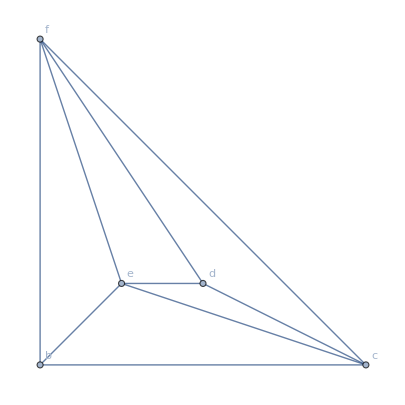

```mathematica
With[{g=VertexDelete[ReadGrof[3],1]},Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->VertexNames[VertexCount[g]+1]]]
```